# Unitarity as a Function of Input Parameters in the Symmetric Phase

```mathematica
Needs["NumericalCalculus`"]
Needs["DifferentialEquations`NDSolveProblems`"];
Needs["DifferentialEquations`NDSolveUtilities`"];
<<MaTeX`
SetOptions[MaTeX,"Preamble"->{"\\usepackage{xcolor, color,txfonts}"}];
```

```mathematica
SetOptions[MaTeX,"Preamble"->{"\\usepackage{xcolor, color, txfonts, amsfonts, amssymb, ulem, amsmath}"},Magnification->1.3];
colors=ColorData[10,"ColorList"];
colorsb=Reverse[ColorData[10, "ColorList"]];
colorsc=ColorData[10, "ColorList"][[5;;]];
tex:=MaTeX;
SetOptions[{Plot,LogPlot,ListLinePlot, ListLogPlot,LogLogPlot,ListPlot,ListLogLinearPlot,ListLogLogPlot,LogLinearPlot,ParametricPlot},
Frame->True, FrameStyle->Black, PlotStyle-> Join[{Black, Blue}, colors, {colors[[1]]}],  ImageSize->350, Background->White, PlotRangePadding->None];
SetDirectory[NotebookDirectory[]];
```

## Formulae from 1805.07306 .

```mathematica
(*Definitions from 1805.07306*)
λ[s_,mi2_, mj2_]:=1/s^2(s^2+mi2^2+mj2^2-2mi2 mj2 -2 s mi2 -2s mj2)(*eq.7*)
modp[s_,mi2_,mj2_]:=1/2 √(s*λ[s,mi2,mj2]) (*eq.8*)
Ei[s_,mi2_,mj2_]:=(s+mi2-mj2)/(2 √s) (*eq.8*)
ft[s_,m12_,m22_,m32_,m42_,m52_]:=1/s 1/(λ[s,m12,m22]*λ[s,m32,m42])^(1/4)Log[(m12+m32-m52-2Ei[s,m12,m22]*Ei[s,m32,m42]+2modp[s,m12,m22]*modp[s,m32,m42])/(m12+m32-m52-2Ei[s,m12,m22]*Ei[s,m32,m42]-2modp[s,m12,m22]*modp[s,m32,m42])](*eq. 9*)

fu[s_,m12_,m22_,m32_,m42_,m52_]:=ft[s,m12,m22,m42,m32,m52](*eq. 9*)

a0[s_]:=-2^(-1/2(delta12+delta34))/(16 π)((λ[s,m12,m22]*λ[s,m32,m42])^(1/4)(λ1234+(κ125*κ345)/(s-m52s))-κ135*κ245 *ft[s,m12,m22,m32,m42,m52t]-κ145*κ235*fu[s,m12,m22,m32,m42,m52u])(*eq. 10*)
```

## Couplings

```mathematica
(*Calculated expressions for the vertices*)
BrokenPhase={λσσηη->λσ+c fpi^(p F-4)((p F)(p F-1)(p F -2)(p F-3))/F^2,(*Numerical factor.?*)
			λσσσσ->3λσ-c fpi^(p F-4)((p F)(p F-1)(p F -2)(p F-3))/F^2,
			ληηηη->3 λσ-c fpi^(p F-4)((p F)(p F-1)(p F -2)(p F-3))/F^2,
			κσηη->λσ*fpi+c fpi^(p F-3)((p F)(p F-1)(p F -2))/F^2,
			κσσσ->3*λσ*fpi-c/F^2 fpi^(p F-3)(p F)(p F-1)(p F-2)};

(*Data from the scattering process. See 'The Question of Unitarity' on DropBox*)
(*This is σ σ->σ σ scattering.*)
ME={λ1234 -> λσσσσ,
κ125 -> κσσσ,
κ345 -> κσσσ,
κ135 -> κσσσ,
κ245 -> κσσσ,
κ145 -> κσσσ,
κ235 -> κσσσ,
delta12 -> 1,
delta34 -> 1,
m12 -> mσ2,
m22 ->mσ2,
m32 -> mσ2,
m42 ->mσ2,
m52u->mσ2,
m52t->mσ2,
m52s->mσ2};
```

```mathematica
nSamples=10000;
(*Fixing fπ now, then using this to set the scale of the problem.*)
fpi=1000;F=3;p=1;
Rangeλa=Array[#&,nSamples,{0,16π}];
Rangeλσ=Array[#&,nSamples,{0,16π/3}];
Rangec=Array[#&,nSamples,{0,16π/3}]*fpi^(4-F p);
```

```mathematica
Samples=Table[{RandomChoice[Rangeλσ],RandomChoice[Rangec]},{i,nSamples}];

(*Check samples are bounded from below*)(*NEED TO DO Fp>4*)
boundingFromBelow[x_]:=(F p<4)||((F p==4)&&(x[[1]]/8>x[[2]]/F^2))
secondMinima[x_]:=((-(p x[[2]])/F(F*p-2)*fpi^(F*p-2)+x[[1]] fpi^2)>0)
secondTrueMinima[x_]:=((-m2/2 fpi^2-(x[[2]] fpi^(F*p))/F^2+x[[1]]/8 fpi^4)/.m2->(-x[[2]]*p/F fpi^(p*F-2)+x[[1]]/2 fpi^2))<0
nonZerom2[x_]:=Abs[(-x[[2]]*p/F fpi^(p*F-2)+x[[1]]/2 fpi^2)]>10(*BAD IR POLES!!!!*)
Samples=Select[Samples,boundingFromBelow];
Samples=Select[Samples,secondMinima];
Samples=Select[Samples,secondTrueMinima];
Samples=Select[Samples,nonZerom2]
```

{(14688 π)/4999,(15840000 π)/4999}

(9408000000 π)/4999

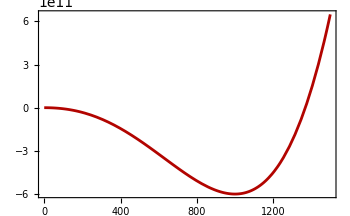

(2064000000 π)/4999

```mathematica
(*TEST POINT*)
y={(14688 π)/4999,(15840000 π)/4999}
((-(p y[[2]])/F(F*p-2)*fpi^(F*p-2)+y[[1]]/1 fpi^2))
Plot[(-m2/2 σ^2-(y[[2]] σ^(F*p))/F^2+y[[1]]/8 σ^4)/.m2->(-y[[2]]*p/F fpi^(p*F-2)+y[[1]]/2 fpi^2),{σ,0,1.5*fpi}]
(-y[[2]]*p/F fpi^(p*F-2)+y[[1]]/2 fpi^2)
```

```mathematica
N[√((2064000000 π)/4999)]
```

1138.91

```mathematica
Sampled = Table[FindMaximum[{Abs[Re[a0[rootS^2]]],Max[2Re[√mσ2],fpi]<rootS<(4*π*fpi)}/.ME/.BrokenPhase/.{λσ->Samples[[i,1]],c->Samples[[i,2]],mσ2->(2-p*F)(Samples[[i,2]]*p)/F fpi^(p F-2)+Samples[[i,1]] fpi^2},{rootS,(3.9*π*fpi)}][[1]],{i,Range[Length[Samples]]}];
```

```mathematica
unitarityContour=Table[{
	Samples[[j]][[1]],
	Samples[[j]][[2]],
	Sampled[[j]]},{j,1,Length[Samples]}];


(*Group rows by first two columns*)
groups=GatherBy[unitarityContour,#[[{1,2}]]&];

(*For each group,select the row with the maximum z*)
maxContour=Map[MaximalBy[#,#[[3]]&][[1]]&,groups];
```

Syntax::stresc: Unknown string escape \l.

Syntax::stresc: Unknown string escape \s.

Syntax::stresc: Unknown string escape \l.

Syntax::stresc: Unknown string escape \s.

Syntax::stresc: Unknown string escape \p.

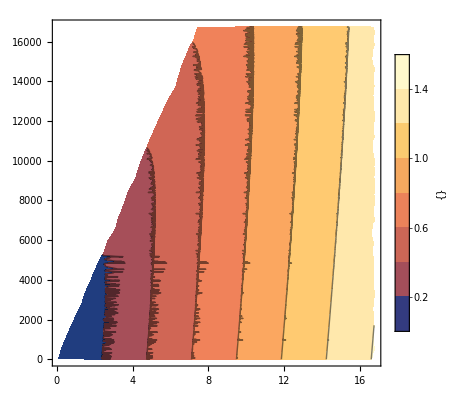

```mathematica
MagPlot=ListContourPlot[maxContour,FrameLabel->{MaTeX["\lambda_\sigma", Magnification->1.3], MaTeX["c", Magnification->1.3]},PlotLegends->BarLegend[Automatic,LegendLabel->{MaTeX["|Re[a_0(4\pi f_\pi)]|",Magnification->1.3]}]]
```